```mathematica
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]];
$HistoryLength=3;
```

Solve the system of differential equations using the Runge-Kutta method and NDSolve, display the solution in one graph.
Use ParametricPlot (NDSolve solution) to create a graph of the dependence of x2 on x1 and ListPlot (Runge-Kutta solution) and display them in one graph.
For all graphs, describe the axes and adjust the PlotStyle. 
exns={x1’(t)=x2(t)-0.1x1(t),x2’(t)=cos(3t)-3x2(t)-x1(t),x1(0)=0,x2(0)=1},
nSteps=25;
tmax=10

```mathematica
Quiet@Remove["Global`*"];
exns={x1'[t]==x2[t]-0.1x1[t],x2'[t]==Cos[3t]-3x2[t]-x1[t],x1[0]==0,x2[0]==1};
tmax=10;
sol=NDSolve[exns,{x1,x2},{t,0,tmax}][[1]];
plotNDSolve=Plot[Evaluate[{x1[t],x2[t]}/.sol],{t,0,tmax},PlotStyle->{Red,Blue},AxesLabel->{"t [s]"," x1  x2  "}];

derivative[{t_,{x1_,x2_}}]:={x2-0.1x1,Cos[3t]-3x2-x1};
nSteps=25;
Δt=N[tmax/nSteps];
initialPoint={0,{0,1}};
RungeKuttaStep[{t_,y_}]:=Module[
{k1,k2,k3,k4},
k1=derivative[{t,y}];
k2=derivative[{t+Δt/2,y+Δt/2*k1}];
k3=derivative[{t+Δt/2,y+Δt/2*k2}];
k4=derivative[{t+Δt,y+Δt*k3}];
{t+Δt,y+Δt/6*(k1+2k2+2k3+k4)}
];
solRungeKutta=NestList[RungeKuttaStep,initialPoint,nSteps];
x1s=solRungeKutta/.{t_,{x1_,x2_}}:>{t,x1};
x2s=solRungeKutta/.{t_,{x1_,x2_}}:>{t,x2};
plX1=ListPlot[x1s,PlotStyle->Black];
plX2=ListPlot[x2s,PlotStyle->Green];
Show[plotNDSolve,plX1,plX2];

ParametricPlot[Evaluate[{x1[t],x2[t]}/.sol],{t,0,tmax},PlotStyle->{Black},AxesLabel->{" x1 ","  x2  "}];
```

Use NMinimize and NMaximize to find the minimum and maximum of the constraint expression.
Display found points and expression graph using Plot3D and ListPlot3D in one graph. 
expr=0.1*(x^2+2x*y+y^2)+x*sin(x+y)+y*Cos(x-y);
constr=(x/1.5)^2+(y/2.5)^2<1.

```mathematica
Quiet@Remove["Global`*"];
expr=0.1*(x^2+2x*y+y^2)+x*Sin[x+y]+y*Cos[x-y];
constr=(x/1.5)^2+(y/2.5)^2<1;
solMin=NMinimize[{expr,constr},{x,y}];
solMax=NMaximize[{expr,constr},{x,y}];
pl1=Plot3D[expr,{x,-2,2},{y,-3,3}];
minPoint={x,y,expr}/.solMin[[2]];
maxPoint={x,y,expr}/.solMax[[2]];
plPoints=ListPointPlot3D[{minPoint,maxPoint},PlotStyle->{Black,PointSize[0.02]}];
Show[pl1,plPoints]
```

{0.13772,-0.767144,-0.515391}

{1.22259,1.44844,2.6794}

-Graphics3D-

```mathematica
Quiet@Remove["Global`*"];

f=50;
ω=2.Pi*f;
T=1/f;
u[t_]:=10*Sin[ω*t]+Sin[3*ω*t]+0.5Sin[5*ω*t];
Plot[u[t],{t,0,3T}];
rn:=1.8*RandomReal[{-1,1}];
dataWithNoise=Table[{t,u[t]+rn},{t,0.,3T,T/1500}];
Export["data.csv",dataWithNoise]
```

data.csv

```mathematica
Quiet@Remove["Global`*"];
SetDirectory[NotebookDirectory[]];
data=Import["data.csv"];
```

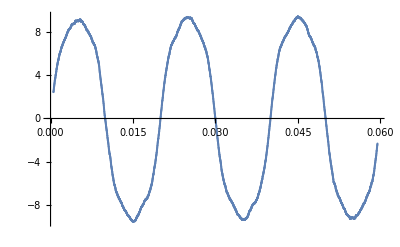

```mathematica
ListPlot[MovingAverage[data,80]]
```

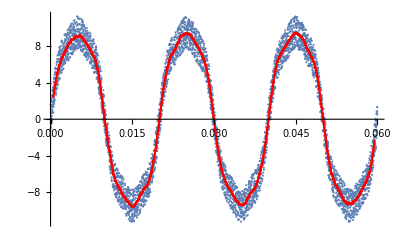

```mathematica
Show[ListPlot[data],ListPlot[MovingAverage[data,80],PlotStyle->Red]]
```

```mathematica
Table[{Subscript[t, i],Subscript[u, i]},{i,1,10,1}]
MovingAverage[%,3]
```

{{t_1,u_1},{t_2,u_2},{t_3,u_3},{t_4,u_4},{t_5,u_5},{t_6,u_6},{t_7,u_7},{t_8,u_8},{t_9,u_9},{t_10,u_10}}

{{1/3 (t_1+t_2+t_3),1/3 (u_1+u_2+u_3)},{1/3 (t_2+t_3+t_4),1/3 (u_2+u_3+u_4)},{1/3 (t_3+t_4+t_5),1/3 (u_3+u_4+u_5)},{1/3 (t_4+t_5+t_6),1/3 (u_4+u_5+u_6)},{1/3 (t_5+t_6+t_7),1/3 (u_5+u_6+u_7)},{1/3 (t_6+t_7+t_8),1/3 (u_6+u_7+u_8)},{1/3 (t_7+t_8+t_9),1/3 (u_7+u_8+u_9)},{1/3 (t_8+t_9+t_10),1/3 (u_8+u_9+u_10)}}

```mathematica
MovingAverage[{a,b,c,d,e},3]
```

{1/3 (a+b+c),1/3 (b+c+d),1/3 (c+d+e)}

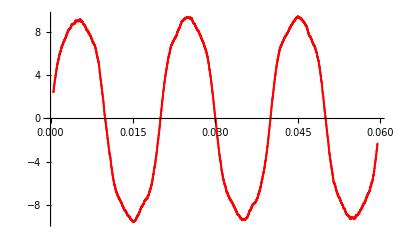

```mathematica
filteredData=MovingAverage[data,80];
ListPlot[MovingAverage[data,80],PlotStyle->Red]
```

```mathematica
intData=Interpolation[filteredData,InterpolationOrder->1];
t1=t/.FindRoot[intData[t]==0,{t,0.01}];
t2=t/.FindRoot[intData[t]==0,{t,0.02}];
t3=t/.FindRoot[intData[t]==0,{t,0.03}];
t4=t/.FindRoot[intData[t]==0,{t,0.04}];
t5=t/.FindRoot[intData[t]==0,{t,0.05}];
periods={t3-t1,t4-t2,t5-t3};
Tint=Mean[periods]
```

0.0200441

```mathematica
Take[filteredData,5]
```

{{0.000526667,2.4555},{0.00054,2.48158},{0.000553333,2.54749},{0.000566667,2.5945},{0.00058,2.66337}}

```mathematica
dat2=Partition[filteredData,2,1];
test[{{t1_,u1_},{t2_,u2_}}]:=u1*u2<0;
selData=Select[dat2,test];
```

{{{0.00991333,0.0363978},{0.00992667,-0.0414788}},{{0.0199933,-0.0214629},{0.0200067,0.0415885}},{{0.02998,0.0447332},{0.0299933,-0.0383129}},{{0.0399933,-0.0983245},{0.0400067,0.00385594}},{{0.0500333,0.0525725},{0.0500467,-0.0154889}}}

```mathematica
selData>>"selData"
```

```mathematica
seld=<<"selData"
```

{{{0.00991333,0.0363978},{0.00992667,-0.0414788}},{{0.0199933,-0.0214629},{0.0200067,0.0415885}},{{0.02998,0.0447332},{0.0299933,-0.0383129}},{{0.0399933,-0.0983245},{0.0400067,0.00385594}},{{0.0500333,0.0525725},{0.0500467,-0.0154889}}}

```mathematica
{{{0.010033333333333333,0.005307220565169807},{0.010046666666666667,-0.07619993442875544}},{{0.019979999999999998,-0.03837182930814568},{0.01999333333333333,0.04146588606699465}},{{0.029979999999999996,0.05766774693921387},{0.02999333333333334,-0.016012699271719055}},{{0.039966666666666664,-0.010617926333274836},{0.039979999999999995,0.02801986395535419}},{{0.05000666666666667,0.015782338916495154},{0.05002,-0.061502575008534094}}}
f1[x_] = Fit[selData[[1]], {1, x}, x];
x1 = x/.FindRoot[f1[x]==0, {x, 0.01}];
f2[x_] = Fit[selData[[2]], {1, x}, x];
x2 = x/.FindRoot[f2[x]==0, {x, 0.02}];
f3[x_] = Fit[selData[[3]], {1, x}, x];
x3 = x/.FindRoot[f3[x]==0, {x, 0.03}];
f4[x_] = Fit[selData[[4]], {1, x}, x];
x4 = x/.FindRoot[f4[x]==0, {x, 0.04}];
f5[x_] = Fit[selData[[5]], {1, x}, x];
x5 = x/.FindRoot[f5[x]==0, {x, 0.05}];
periods2={x3-x1,x4-x2,x5-x3};
Tint2=Mean[periods2];
Tint == Tint2
```

{{{0.0100333,0.00530722},{0.0100467,-0.0761999}},{{0.01998,-0.0383718},{0.0199933,0.0414659}},{{0.02998,0.0576677},{0.0299933,-0.0160127}},{{0.0399667,-0.0106179},{0.03998,0.0280199}},{{0.0500067,0.0157823},{0.05002,-0.0615026}}}

0.0200441

True